```mathematica
Simplify[Solve[Ecm == √(q^2+mp^2) + √(q^2+mj^2), q]]
```

{{q→-(√(Ecm^4+(mj^2-mp^2)^2-2 Ecm^2 (mj^2+mp^2)))/(2 Ecm)},{q→(√(Ecm^4+(mj^2-mp^2)^2-2 Ecm^2 (mj^2+mp^2)))/(2 Ecm)}}

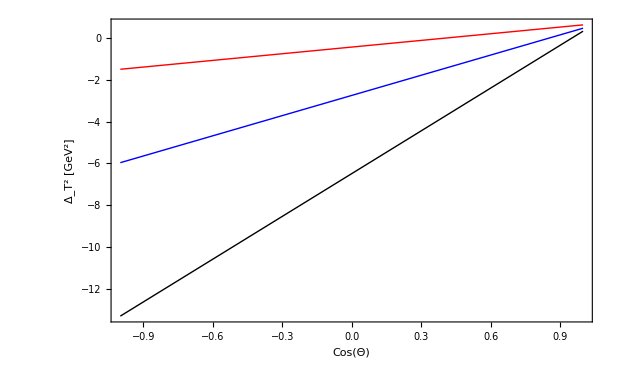

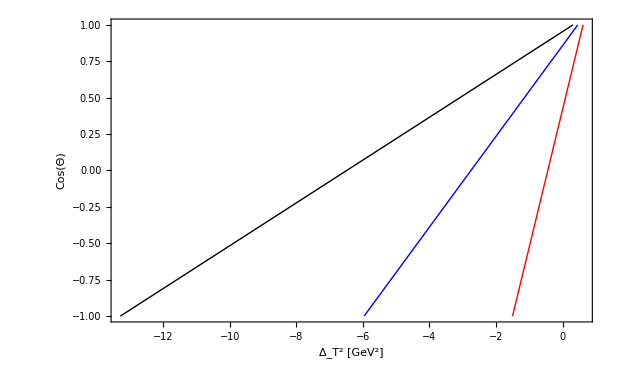

{-1.50406,-0.443789,0.616486}

{-5.96462,-2.75368,0.457248}

{-13.2926,-6.48861,0.31538}

```mathematica
Mpi = 0.135;
MN = 0.938;
Mj = 3.096;
s[plab_] := 2 MN^2+2 MN √(MN^2+plab^2)
pcm[plab_] :=plab MN/(√s[plab])
q[plab_] := (√(s[plab]^2+(Mj^2-Mpi^2)^2-2 s[plab](Mj^2+Mpi^2)))/(2 √s[plab]) 
t[cth_, plab_] :=( (√(q[plab]^2+Mpi^2) - √(pcm[plab]^2+MN^2))^2- pcm[plab]^2- q[plab]^2 +(2q[plab]pcm[plab])cth)

t_th[theta_, plab_] := t[Cos[theta], plab]

costh[t_, plab_] := (t+ pcm[plab]^2+ q[plab]^2- (√(q[plab]^2+Mpi^2) - √(pcm[plab]^2+MN^2))^2 )/(2q[plab]pcm[plab])

theta[t_,plab_] := ArcCos[costh[t,plab]]

p0 = Plot[ t[ct, 5.513], {ct, -1.0, 1.0}, PlotRange->All, PlotStyle->{Red, Thick}];
p1 = Plot[ t[ct, 8], {ct, -1.0, 1.0}, PlotRange->All, PlotStyle->{Blue, Thick}];
p2 = Plot[ t[ct, 12], {ct, -1.0, 1.0}, PlotRange->All, PlotStyle->{Black, Thick}];
pinv0 = Plot[ costh[tt, 5.513], {tt, t[-1, 5.513], t[1,5.513]}, PlotRange->All, PlotStyle->{Red, Thick}];
pinv1 = Plot[ costh[tt, 8.0], {tt, t[-1, 8.0], t[1,8.0]}, PlotRange->All, PlotStyle->{Blue, Thick}];pinv2= Plot[ costh[tt, 12.0], {tt, t[-1, 12.0], t[1,12.0]}, PlotRange->All, PlotStyle->{Black, Thick}];

pinvth0 = Plot[ theta[tt, 5.513], {tt, t[-1, 5.513], t[1,5.513]}, PlotRange->All, PlotStyle->{Red, Thick}];
pinvth1 = Plot[ theta[tt, 8.0], {tt, t[-1, 8.0], t[1,8.0]}, PlotRange->All, PlotStyle->{Blue, Thick}];pinvth2= Plot[ theta[tt, 12.0], {tt, t[-1, 12.0], t[1,12.0]}, PlotRange->All, PlotStyle->{Black, Thick}];

Show[{p0, p1, p2}, Frame->True, FrameStyle->Directive[FontSize->10,FontFamily->"TimesNewRoman"], FrameLabel->{"Cos(Θ)","Δ_T^2  [GeV^2]"} ]
Show[{pinv0, pinv1, pinv2},Frame->True,FrameStyle->Directive[FontSize->10,FontFamily->"TimesNewRoman"], FrameLabel->{"Δ_T^2  [GeV^2]", "Cos(Θ)"} ]
(* Show[{pinvth0, pinvth1, pinvth2}] *)

{t[-1,5.513], t[0,5.513],t[1,5.513]}
{t[-1,8],t[0,8],t[1,8]}
{t[-1,12], t[0,12],t[1,12]}
```